## Distribution of states at steady state

```mathematica
Nm = 13;
```

#### Distributions for N = 6.5

```mathematica
data6J0=Import["/media/luke/Elements/Simulations/Without _depletion/Glauber/Initial_conditions_J=0.00_N=65.dat"];
data6J3=Import["/media/luke/Elements/Simulations/Without _depletion/Glauber/Initial_conditions_J=3.00_N=65.dat"];
data6J5=Import["/media/luke/Elements/Simulations/Without _depletion/Glauber/Initial_conditions_J=5.00_N=65.dat"];
```

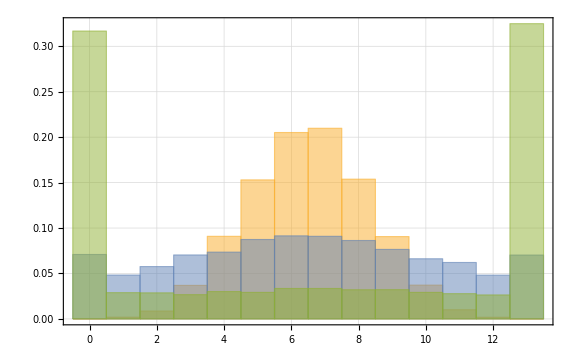

```mathematica
Histogram[{data6J0[[All,1]]*Nm,data6J3[[All,1]]*Nm,data6J5[[All,1]]*Nm},Automatic,"Probability",ImageSize->Large,Frame->True,GridLines->Automatic]
```

```mathematica
Ndata6J0 = data6J0[[All,1]]*Nm;
Ndata6J3 = data6J3[[All,1]]*Nm;
Ndata6J5 = data6J5[[All,1]]*Nm;
```

```mathematica
est6J0=FindDistribution[Ndata6J0, TargetFunctions->{NormalDistribution}];
est6J3 = FindDistribution[Ndata6J3, TargetFunctions->{GammaDistribution,NormalDistribution,CauchyDistribution}];
est6J5 = FindDistribution[Ndata6J5,TargetFunctions->{CauchyDistribution,NormalDistribution}]
```

MixtureDistribution[{0.523275,0.476725},{CauchyDistribution[0.0821353,0.459303],CauchyDistribution[12.9387,0.450833]}]

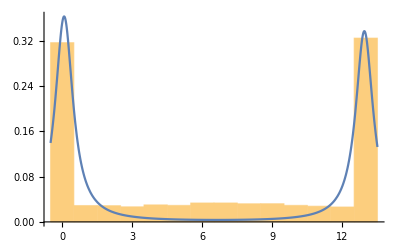

```mathematica
Show[Histogram[Ndata6J5,Automatic,"ProbabilityDensity"],Plot[PDF[est6J5,x],{x,-0.5,Nm+0.5},PlotRange->All]]
```

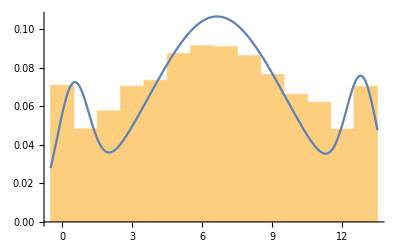

```mathematica
Show[Histogram[Ndata6J3,Automatic,"ProbabilityDensity"],Plot[PDF[MixtureDistribution[{0.10465177530362536,0.7841051268806382,0.11124309781573656},{NormalDistribution[0.4748598829510297,0.6908769535881998],NormalDistribution[6.629277877556958,2.9343992982288665],NormalDistribution[12.839797496932285,0.6908769535881998]}],x],{x,-0.5,Nm+0.5},PlotRange->All]]
```

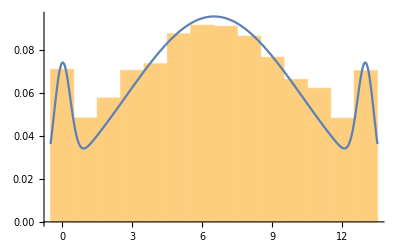

```mathematica
Show[Histogram[Ndata6J3,Automatic,"ProbabilityDensity"],Plot[PDF[MixtureDistribution[{200,4000,200},{NormalDistribution[0,0.35],NormalDistribution[6.5,3.8],NormalDistribution[13,0.35]}],x],{x,-0.5,Nm+0.5},PlotRange->All]]
```

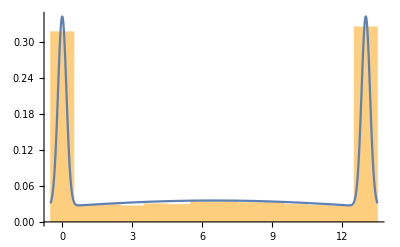

```mathematica
Show[Histogram[Ndata6J5,Automatic,"ProbabilityDensity"],Plot[PDF[MixtureDistribution[{1,5,1},{NormalDistribution[0,0.18],NormalDistribution[6.5,8],NormalDistribution[13,0.18]}],x],{x,-0.5,Nm+0.5},PlotRange->All]]
```

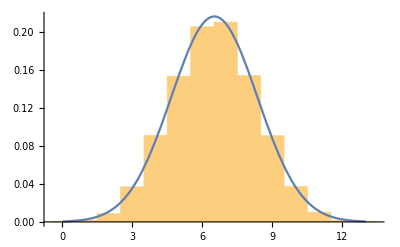

```mathematica
Show[Histogram[Ndata6J0,Automatic,"Probability"],Plot[PDF[est6J0,x],{x,0,Nm}]]
```

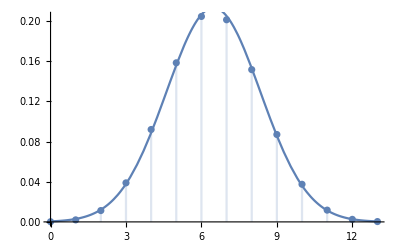

```mathematica
Show[DiscretePlot[PDF[BinomialDistribution[14,0.46263],k],{k,0,Nm}],Plot[PDF[NormalDistribution[6.47682,1.87],x],{x,0,Nm}]]
```

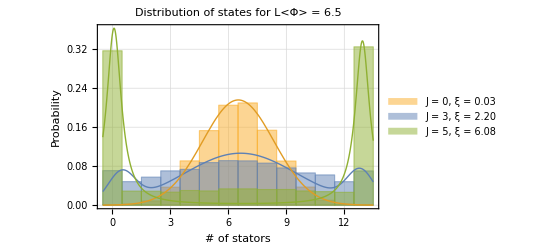

```mathematica
Show[Histogram[{data6J0[[All,1]]*Nm,data6J3[[All,1]]*Nm,data6J5[[All,1]]*Nm},Automatic,"Probability",ImageSize->Full,Frame->True,GridLines->Automatic, ChartLegends->{Placed[{Text[Style["J = 0, ξ = 0.03",30]],Text[Style["J = 3, ξ = 2.20",30]],Text[Style["J = 5, ξ = 6.08",30]]},{{0.5,0.87},{0.5,0.5}}]},FrameLabel->{"# of stators", "Probability"},LabelStyle->Directive[25,Black],PlotLabel->"Distribution of states for L<Φ> = 6.5"],Plot[{PDF[MixtureDistribution[{0.10465177530362536,0.7841051268806382,0.11124309781573656},{NormalDistribution[0.4748598829510297,0.6908769535881998],NormalDistribution[6.629277877556958,2.9343992982288665],NormalDistribution[12.839797496932285,0.6908769535881998]}],x],PDF[est6J0,x],PDF[est6J5,x]},{x,-0.5,Nm+0.5},PlotRange->All,PlotStyle->Thick]]
```

#### Distribution for N = 4

```mathematica
data4J0=Import["/media/luke/Elements/Simulations/Without _depletion/Glauber/Initial_conditions_J=0.00_N=4.dat"];
data4J3=Import["/media/luke/Elements/Simulations/Without _depletion/Glauber/Initial_conditions_J=3.00_N=4.dat"];
data4J5=Import["/media/luke/Elements/Simulations/Without _depletion/Glauber/Initial_conditions_J=5.00_N=4.dat"];
```

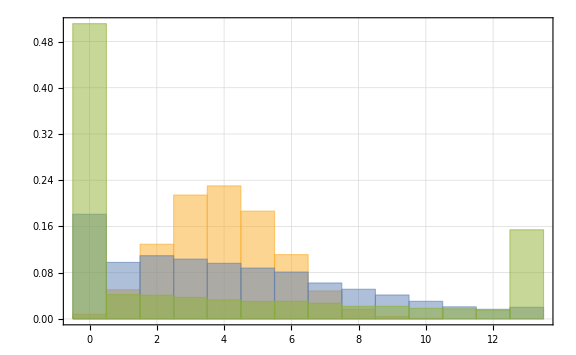

```mathematica
Histogram[{data4J0[[All,1]]*Nm,data4J3[[All,1]]*Nm,data4J5[[All,1]]*Nm},Automatic,"Probability",ImageSize->Large,Frame->True,GridLines->Automatic]
```

```mathematica
Ndata4J0 = data4J0[[All,1]]*Nm;
Ndata4J3 = data4J3[[All,1]]*Nm;
Ndata4J5 = data4J5[[All,1]]*Nm;
```

```mathematica
est4J0=FindDistribution[Ndata4J0,TargetFunctions->{NormalDistribution}]
est4J3 = FindDistribution[Ndata4J3,TargetFunctions->{NormalDistribution}]
est4J5 = FindDistribution[Ndata4J5, TargetFunctions->"Continuous",TargetFunctions->{NormalDistribution}];
```

NormalDistribution[3.99461,1.69623]

MixtureDistribution[{0.21132,0.264891,0.41459,0.109198},{NormalDistribution[0.103139,0.378954],NormalDistribution[2.0444,0.957901],NormalDistribution[5.70516,1.9918],NormalDistribution[10.7234,1.45399]}]

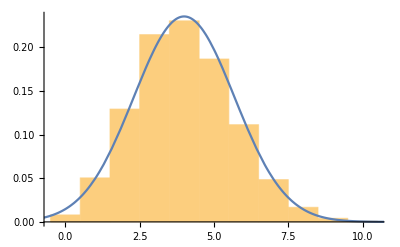

```mathematica
Show[Histogram[Ndata4J0,Automatic,"Probability"],Plot[PDF[est4J0,x],{x,-1,Nm}]]
```

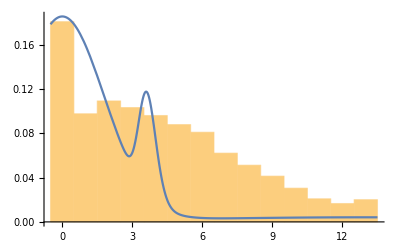

```mathematica
Show[Histogram[Ndata4J3,Automatic,"ProbabilityDensity"],Plot[PDF[MixtureDistribution[{10,1,1},{NormalDistribution[0,1.8],LogNormalDistribution[0,0.1],NormalDistribution[13,8]}],x],{x,-0.5,Nm+0.5},PlotRange->All]]
```

```mathematica
Plot[PDF[MixtureDistribution[{1,1,1},{NormalDistribution[0,0.15],LogNormalDistribution[],NormalDistribution[13,3.5]}],x],{x,-0.5,Nm+0.5},PlotRange->All]
```

-Graphics-

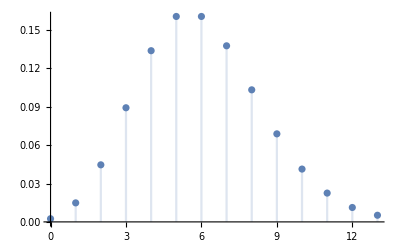

```mathematica
DiscretePlot[PDF[PoissonDistribution[6],x],{x,0,Nm}]
```